#### Utils

```mathematica
sampleDetRoot[det_,initList_]:=
First@MaximalBy[Quiet@Check[σ/.FindRoot[det,{σ,#}],-100-I]&/@initList,Re]
```

```mathematica
findDispRel[M_,params_,eq_,qRange_:{_,_,_}]:=With[{
MParams=M/.eq/.params
},
Table[
{qIter,sampleDetRoot[Det[MParams/.q->qIter],{0.1,0.1+0.1I,0.5,0.5+I,1.,1.+I,5.,5.+I,10.,10.+I,20.}]},
{qIter,Range@@qRange}
]
]
```

```mathematica
findDispRel[M_,params_,eq_,qRange_:{_,_,_},
"ApproxJacobian"->(approxJ_?MatrixQ)
]:=With[{
MParams=M/.eq/.params,
JApproxParams=approxJ/.eq/.params
},
Table[{
qIter,
σ/.FindRoot[
Det[MParams/.q->qIter],
{σ,First@MaximalBy[Eigenvalues[JApproxParams/.q->qIter],Re]},
Evaluated->False
]
},
{qIter,Range@@qRange}
]]
```

```mathematica
findLineDispRel[J_,params_,eq_,qRange_:{_,_,_}]:=With[{
JParams=J/.eq/.params
},
Table[
{qIter,First@MaximalBy[Eigenvalues[JParams/.q->qIter],Re]},
{qIter,Range@@qRange}
]
]
```

```mathematica
plotDispRel[dispRel_]:=ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@dispRel],
Joined->True,
AxesLabel->{q,σ},
PlotLegends->{"Re(σ)","Im(σ)"}
]
```

#### Model setup

```mathematica
f=-kr m^2 c+m;
r=kr m^2 c-m;
```

```mathematica
Jreact=D[{r,f},{{m,c}}];
```

```mathematica
params={n->3,kr->0.1,h->10,Dc->10,Dm->0.1};
```

#### Laterally homogeneous steady state

```mathematica
hssEqns={
r,m+h c-h n
};
```

```mathematica
nSolveHSSEqns[params_]:=SortBy[Cases[
Chop@NSolve[
hssEqns/.params,
{m,c}
],
{HoldPattern[_->(_?(Im@#==0&&#≥0&))]..}
],
First
]
```

```mathematica
hssList=nSolveHSSEqns[params]
```

{{m→0,c→3.},{m→3.81966,c→2.61803},{m→26.1803,c→0.381966}}

#### Linear stability analysis

```mathematica
Γ[σ_,q_]:=-√(q^2+σ/Dc)Tanh[√(q^2+σ/Dc)h]
```

```mathematica
M=Jreact+DiagonalMatrix[{-σ-q^2 Dm,Dc Γ[σ,q]}];
```

```mathematica
dispRel=findDispRel[M,params,Last@hssList,{0,2,0.05}];
```

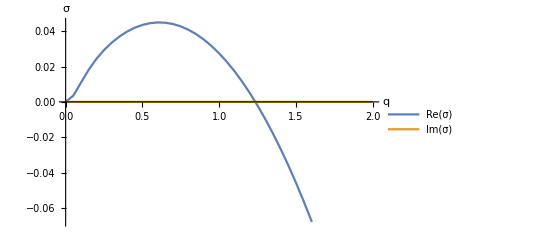

```mathematica
plotDispRel@dispRel
```

### Slow growth rate approximation

Develop the matrix M(σ) to first order in σ

```mathematica
M0=M/.σ->0
```

{{-1+2 c kr m-Dm q^2,kr m^2},{1-2 c kr m,-kr m^2-Dc √(q^2) Tanh[h √(q^2)]}}

```mathematica
M1=D[M,σ]/.σ->0
```

{{-1,0},{0,-1/2 h Sech[h √(q^2)]^2-Tanh[h √(q^2)]/(2 √(q^2))}}

We can then construct an eigenvalue problem for σ that yields the approximate solutions of M(σ)e=0:
Expand M

	0=M(σ)e≈(M_0+M_1 σ)e

Now multiply with M_1^-1 from the left

	(M_1^-1 M_0+σ)e≈0

Thus, the eigenvalues and eigenvectors of -M_1^-1 M_0 approximate the solution pairs (σ,e) of M(σ)e=0.

Note that M_1 becomes singular for q→0. Thus, the approximation only works for q≠0.

```mathematica
approxJacobian=-Inverse[M1].M0;
```

```mathematica
dispRelApprox=findLineDispRel[approxJacobian,params,Last@hssList,{0.05,2,0.05}];
```

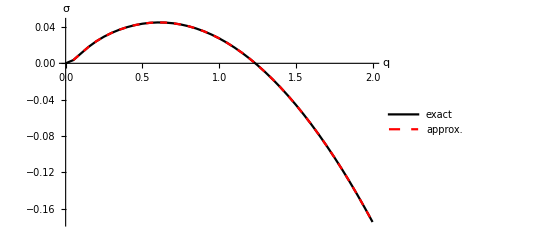

```mathematica
ListLinePlot[{
Re@dispRel,
Re@dispRelApprox
},
PlotStyle->{Black,Directive[Dashed,Red]},
AxesLabel->{q,σ},
PlotLegends->{"exact","approx."}
]
```

#### Failure of slow growth rate approximtion for large growth rates and small wavenumbers

```mathematica
params={n->3,kr->0.1,h->10,Dc->10,Dm->0.1};
hssList=nSolveHSSEqns[params]
```

{{m→0,c→3.},{m→3.81966,c→2.61803},{m→26.1803,c→0.381966}}

Calculate dispersion relation for the second fixed point which is unstable against homogeneous perturbations (q=0)

```mathematica
dispRel=findDispRel[M,params,hssList[[2]],{0,1,0.02}];
dispRelApprox=findLineDispRel[approxJacobian,params,hssList[[2]],{0.01,1,0.01}];
```

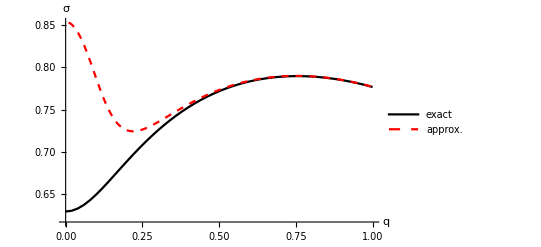

```mathematica
ListLinePlot[{
Re@dispRel,
Re@dispRelApprox
},
PlotStyle->{Black,Directive[Dashed,Red]},
AxesLabel->{q,σ},
PlotLegends->{"exact","approx."}
]
```